```mathematica
F[{x_,y_},r_]:=Module[{a=x+I y},
Return[{Re[r[a]],Im[r[a]]}]]
```

```mathematica
G[{x_,y_},r_]:=Line[{{x,y},F[{x,y},r]}]
```

```mathematica
G[{-3,-3},#^2&]
```

Line[{{-3,-3},{0,18}}]

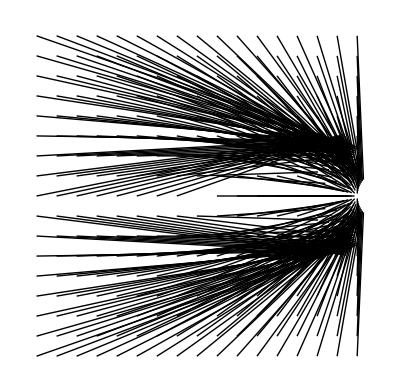
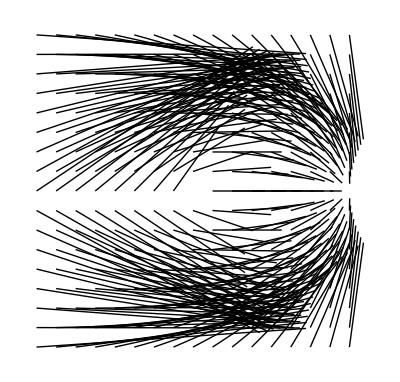
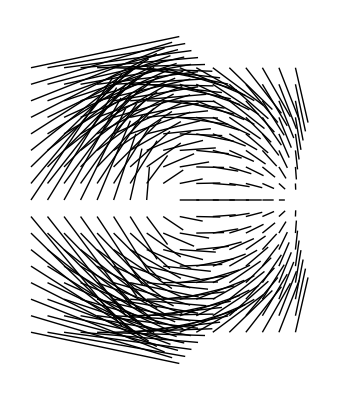
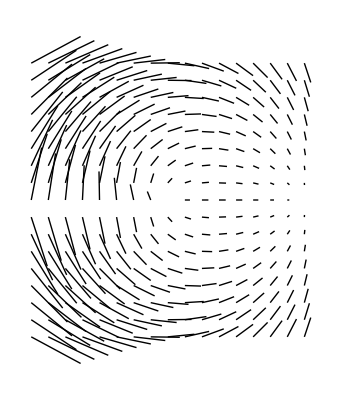
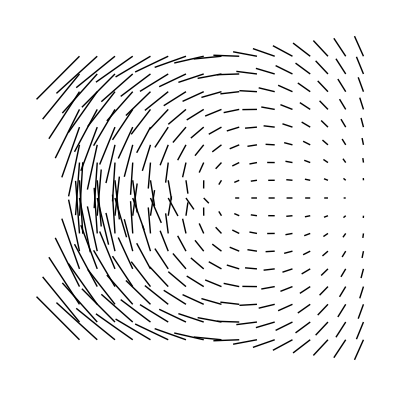
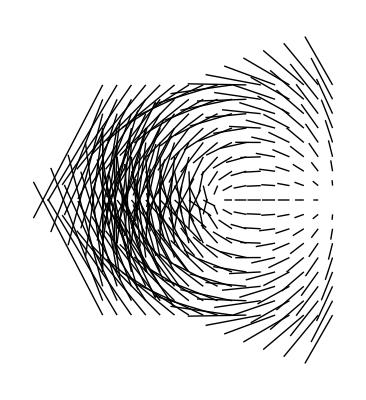
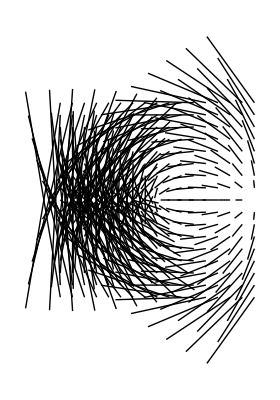
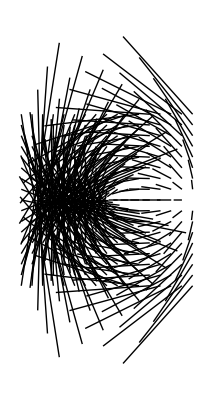

```mathematica
Table[Graphics[Table[G[{x,y},#^s&],{x,-1,1,.125},{y,-1,1,.125}]],{s,.125,15,.25}]
```

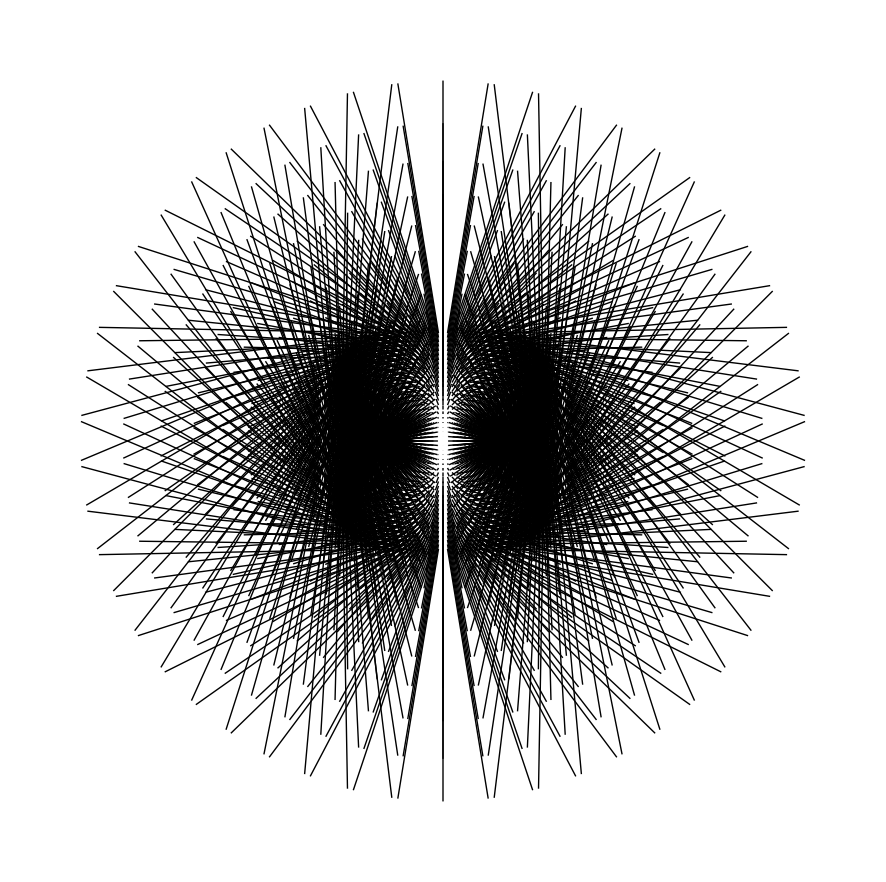

```mathematica
Graphics[Table[G[{x,y},Sin[#]&],{x,-3,3,.125},{y,-3,3,.125}]]
```